```mathematica
dists=PlanetData[{Entity["Planet","Mercury"],Entity["Planet","Mars"]},Table[EntityProperty["Planet","DistanceFromEarth",{"Date"->date}],{date,DateRange[{2019,1,9},{2022,2,24},"Week"]}],"EntityAssociation"];
```

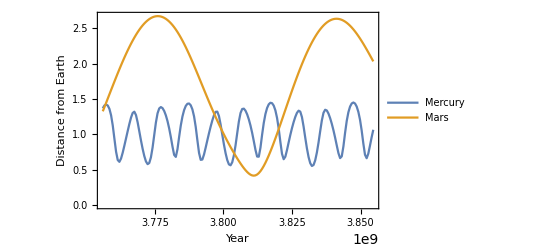

```mathematica
DateListPlot[dists,{{2019,1,9},{2022,2,24}}, FrameLabel->{{"Distance from Earth", None}, {"Year", None}}]
```